```mathematica
RK4[f_,t0_,T_,u0_,h_]:=Module[{
n=⌈(T-t0)/h⌉,t,res,i,s,
a=N@{0,1/2,1/2,1},b=N@{0,1/2,1/2,1},p=N@{1/3,1/6,1/6,1/3},k=ConstantArray[0,4]},
t=Table[t0+k*h,{k,0,n}];
res=ConstantArray[0,n+1];
res⟦1⟧=u0;

For[i=1,i≤n,i++,
For[s=1,s≤4,s++,
k⟦s⟧=h*f[t⟦i⟧+a⟦s⟧h,res⟦i⟧+b⟦s⟧ k⟦s-1⟧];
];
res⟦i+1⟧=res⟦i⟧+p.k;
];

{t,res}
]

AB4Droplet[f_,s0_,u0_,h_]:=Module[{
s=Table[s0+k h,{k,0,3}],coeffs,func,res},
res=RK4[f,s0,s0+3 h,u0,h]⟦2⟧;
func=MapThread[f,{s,res}];
coeffs=N@{-3/8,37/24,-59/24,55/24};

While[res⟦-1,1⟧<1,
AppendTo[s,s⟦-1⟧+h];
AppendTo[res,res⟦-1⟧+h coeffs.func];
func=RotateLeft[func,1];
func⟦4⟧=f[s⟦-1⟧,res⟦-1⟧];
];

{s,res}
]
```

```mathematica
(* Example *)
b=1.84366;
c=-2.9;
f[s_,u_List]:={Cos@u⟦3⟧,Sin@u⟦3⟧,If[s==0,b,2 b+c u⟦2⟧-(Sin@u⟦3⟧)/u⟦1⟧]};
s0=0;
u0={0,0,0};
h=0.001;
```

```mathematica
(* Approximation *)
{s,u}=AB4Droplet[f,s0,u0,h];
```

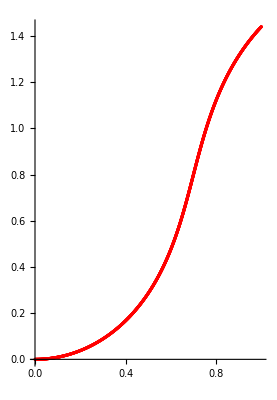

```mathematica
ListPlot[u⟦All,{1,2}⟧,PlotStyle->Red,AspectRatio->Full]
```